```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
<<BISfit`;
<<Data`;
<<Matcher`;
```

```mathematica
data=nxrData[];
Dimensions[data]
```

{50,2,138,2}

```mathematica
ffdata=Flatten[data,{{1},{2},{3,4}}];
fdata=ffdata;
Dimensions[fdata]
```

{50,2,276}

```mathematica
(* first test raw data,all features*)
```

```mathematica
{ddiff,dsame}=eucDist[fdata];
```

```mathematica
md=Mean[ddiff]
ddd=StandardDeviation[ddiff]
ms=Mean[dsame]
dds=StandardDeviation[dsame]
```

7081.42

5120.79

2029.83

3725.19

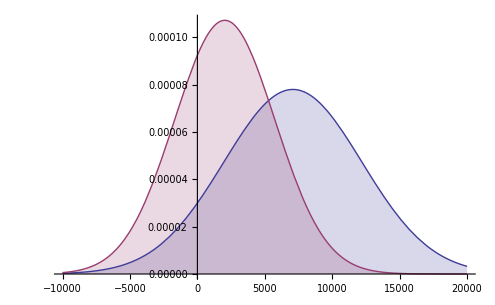

```mathematica
Plot[{PDF[NormalDistribution[md,ddd],x],PDF[NormalDistribution[ms,dds],x]},{x,-10000,20000},Filling->Axis]
```

```mathematica
{ns,nd}={Length[dsame],Length[ddiff]}
```

{50,4900}

```mathematica
(* this is the t value*)
d=(Mean[ddiff]-Mean[dsame])/(√(Variance[ddiff]/(Length[ddiff])+Variance[dsame]/(Length[dsame])))
```

9.49767

SignificanceLevel means the odds of saying H1 is true when in fact H0 is.

It seems ddiff and dsame should never be the same.

```mathematica
r=TTest[{ddiff,dsame},0,{"ShortTestConclusion"},SignificanceLevel->0.00001]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 5.×10^-6. The tests in {"T"} require that the data is normally distributed.

{Reject}

```mathematica
(*assume H0-> dsame==0?*)
```

```mathematica
ds=(Mean[dsame]-2000)/(√(Variance[dsame]/(Length[dsame])))
```

0.0566236

The inner class distance is not 0... but 2000

```mathematica
TTest[dsame,0,{"TestDataTable","TestConclusion"}]
```

TTest::nortst: At least one of the p-values in 0., resulting from a test for normality, is below 0.05. The tests in {"T"} require that the data is normally distributed.

Intersection::normal: Nonatomic expression expected at position 2 in {"PairedT", "PairedZ", "T", "Z"} ∩ "T".

TTest::nortst: At least one of the p-values in 0., resulting from a test for normality, is below 0.05. The tests in {"PairedT", "PairedZ", "T", "Z"} ∩ "T" require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{ | Statistic | P-Value
T | 3.85298 | 0.000339495,The null hypothesis that the median of the population is equal to 0 is rejected at the 5. percent level based on the T test.}

```mathematica
TTest[dsame,2000,{"TestDataTable","TestConclusion"}]
```

TTest::nortst: At least one of the p-values in 0., resulting from a test for normality, is below 0.05. The tests in {"T"} require that the data is normally distributed.

Intersection::normal: Nonatomic expression expected at position 2 in {"PairedT", "PairedZ", "T", "Z"} ∩ "T".

TTest::nortst: At least one of the p-values in 0., resulting from a test for normality, is below 0.05. The tests in {"PairedT", "PairedZ", "T", "Z"} ∩ "T" require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{ | Statistic | P-Value
T | 0.0566236 | 0.955075,The null hypothesis that the median of the population is equal to 2000 is not rejected at the 5. percent level based on the T test.}

```mathematica
h=TTest[dsame,2000,"HypothesisTestData"];
h["Properties"]
```

{DegreesOfFreedom,HypothesisTestData,PValue,PValueTable,ShortTestConclusion,TestConclusion,TestData,TestDataTable,TestStatistic,TestStatisticTable}

```mathematica
h["DegreesOfFreedom"]
```

49

```mathematica
(* now std data,passed*)
```

```mathematica
data=nxrData[-1];
Dimensions[data]
```

{50,2,6,46}

```mathematica
ffdata=Flatten[data,{{1},{2},{3,4}}];
Dimensions[%]
```

{50,2,276}

```mathematica
{ddiff,dsame}=eucDist[ffdata];
```

```mathematica
md=Mean[ddiff]
ddd=StandardDeviation[ddiff]
ms=Mean[dsame]
dds=StandardDeviation[dsame]
```

19.7108

12.985

4.64431

5.69154

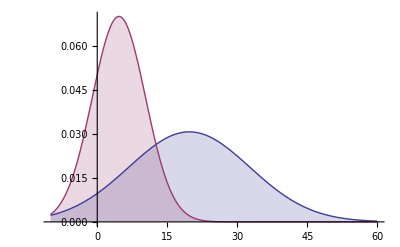

```mathematica
Plot[{PDF[NormalDistribution[md,ddd],x],PDF[NormalDistribution[ms,dds],x]},{x,-10,60},Filling->Axis]
```

```mathematica
r=TTest[{ddiff,dsame},15,{"ShortTestConclusion"},SignificanceLevel->0.001]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.0005. The tests in {"T"} require that the data is normally distributed.

{Do not reject}

```mathematica
Table[TTest[{ddiff,dsame},i,{"ShortTestConclusion"},SignificanceLevel->0.001],{i,12.5,17.5,0.5}]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.0005. The tests in {"T"} require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject}}

difference in 15±2.5,donot reject

```mathematica
TTest[dsame,19,{"TestDataTable","TestConclusion"}]
```

TTest::nortst: At least one of the p-values in 0., resulting from a test for normality, is below 0.05. The tests in {"T"} require that the data is normally distributed.

Intersection::normal: Nonatomic expression expected at position 2 in {"PairedT", "PairedZ", "T", "Z"} ∩ "T".

TTest::nortst: At least one of the p-values in 0., resulting from a test for normality, is below 0.05. The tests in {"PairedT", "PairedZ", "T", "Z"} ∩ "T" require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{ | Statistic | P-Value
T | -17.8352 | 4.54083×10^-23,The null hypothesis that the median of the population is equal to 19 is rejected at the 5. percent level based on the T test.}

```mathematica
(* test block*)
```

```mathematica
BlockRandom[SeedRandom[1];data1=RandomVariate[NormalDistribution[0.5,0.5],1000];
data2=RandomVariate[NormalDistribution[0,1],1000]];
h=TTest[{data1,data2},Automatic,"HypothesisTestData"]
```

5.74384×10^-37

```mathematica
h["TestStatisticTable"]
```

| Statistic
T | 13.0658

```mathematica
(* what we should really do is to test each feature*)
```

```mathematica
(* first use each freq point of each method,totoal 276, only a few passed*)
```

```mathematica
{ddv,dsv}=eucDistV[fdata];
```

```mathematica
Dimensions[ddv]
```

{4900,276}

```mathematica
d1=ddv[[;;,1]];
s1=dsv[[;;,1]];
```

```mathematica
Dimensions[d1]
```

{4900}

```mathematica
TTest[{d1,s1},Automatic,{"ShortTestConclusion"},SignificanceLevel->0.001]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.0005. The tests in {"T"} require that the data is normally distributed.

{Do not reject}

```mathematica
t1=AbsoluteTime[];
rr=Table[TTest[{ddv[[;;,i]],dsv[[;;,i]]},Automatic,{"ShortTestConclusion"},SignificanceLevel->0.001],{i,Length[ddv[[1]]]}];
t2=AbsoluteTime[]-t1
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.0005. The tests in {"T"} require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

```mathematica
38.96875`9.04226146865461
```

```mathematica
Length[Select[rr,#=={"Reject"}&]]
```

68

```mathematica
rr[[5]]=={"Do not reject"}
```

True

```mathematica
rr
```

{{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Reject},{Reject},{Reject},{Reject},{Reject},{Do not reject},{Reject},{Reject},{Reject},{Reject},{Reject},{Do not reject},{Reject},{Reject},{Reject},{Reject},{Reject},{Do not reject},{Reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Reject},{Do not reject},{Do not reject},{Do not reject},{Reject},{Do not reject},{Reject},{Reject},{Reject},{Reject},{Reject},{Reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject}}

```mathematica
(*then each method,Passed*)
```

```mathematica
pdata=
Partition[ffdata,{1,1,46}];
Dimensions[pdata];

pd=Flatten[pdata,{{1},{2},{3},{4,5,6}}];
Dimensions[%]
```

{50,2,6,46}

```mathematica
rr=Table[TTest[eucDist[pd[[All,All,i]]],Automatic,{"TestStatistic","ShortTestConclusion"},SignificanceLevel->0.001],{i,6}]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.0005. The tests in {"T"} require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{{10.5722,Reject},{20.9411,Reject},{16.7778,Reject},{24.5171,Reject},{18.3686,Reject},{17.91,Reject}}

The mehtod order is 4, 2, 5, 6, 3, 1.

```mathematica
(*then each freq,Passed,*)
```

```mathematica
ff=Freq23[];
```

```mathematica
pd=Table[Flatten[data[[All,All,All,{i,i+1}]],{{1},{2},{3,4}}],{i,23}];
Dimensions[pd]
```

{23,50,2,12}

```mathematica
rr=Table[TTest[eucDist[pd[[i]]],Automatic,{"TestStatistic","ShortTestConclusion"},SignificanceLevel->0.001],{i,23}]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.0005. The tests in {"T"} require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{{9.5822,Reject},{10.7743,Reject},{15.0347,Reject},{16.4052,Reject},{18.2416,Reject},{16.4772,Reject},{11.4778,Reject},{14.2966,Reject},{21.0476,Reject},{24.2408,Reject},{20.3623,Reject},{21.3612,Reject},{19.4403,Reject},{19.161,Reject},{18.9419,Reject},{19.1242,Reject},{18.3547,Reject},{18.8987,Reject},{19.5823,Reject},{19.6362,Reject},{19.843,Reject},{19.0782,Reject},{17.7777,Reject}}

```mathematica
Ordering[rr[[;;,1]]]
```

{1,2,7,8,3,4,6,23,5,17,18,15,22,16,14,13,19,20,21,11,9,12,10}